# Comet Mission: 1998P/Willis

## Part 2: Comet Properties:

```mathematica
a=4000;(*meters*)
b=2000;(*meters*)
c=1500;(*meters*)
nucleus=(x^2/a^2)+(y^2/b^2)+(z^2/c^2);
Plot1=ContourPlot3D[nucleus==1,{x,-a,a},{y,-b,b},{z,-c,c},BoxRatios->{a/c,b/c,1},Mesh->None,ContourStyle->{Gray},PlotLabel->"Comet 1998P/Willis",AxesLabel->{"x(m)","y(m)","z(m)"}]
```

-Graphics3D-

```mathematica
Subscript[p, comet]=400;(*mass density of comet in kg/m^3*)
```

## 2a: Mass of Comet’s Nucleus

```mathematica
Mass=NIntegrate[400,{x,-a,a},{y,-√(b^2(1-(x^2/a^2))),√(b^2(1-(x^2/a^2)))},{z,-√(c^2(1-(x^2/a^2)-(y^2/b^2))),√(c^2(1-(x^2/a^2)-(y^2/b^2)))}](*mass of comet in Kg/m^3*)
```

2.01062×10^13

## 2b: Moment of Inertia

```mathematica
Subscript[I, x]=NIntegrate[Subscript[p, comet]*((y^2)+(z^2)),{x,-a,a},{y,-√(b^2(1-(x^2/a^2))),√(b^2(1-(x^2/a^2)))},{z,-√(c^2(1-(x^2/a^2)-(y^2/b^2))),√(c^2(1-(x^2/a^2)-(y^2/b^2)))}](*moment about x-axis*)
```

2.51327×10^19

```mathematica
Subscript[I, y]=NIntegrate[Subscript[p, comet]*((x^2)+(z^2)),{x,-a,a},{y,-√(b^2(1-(x^2/a^2))),√(b^2(1-(x^2/a^2)))},{z,-√(c^2(1-(x^2/a^2)-(y^2/b^2))),√(c^2(1-(x^2/a^2)-(y^2/b^2)))}](*moment about y-axis*)
```

7.33876×10^19

```mathematica
Subscript[I, z]=NIntegrate[Subscript[p, comet]*((x^2)+(y^2)),{x,-a,a},{y,-√(b^2(1-(x^2/a^2))),√(b^2(1-(x^2/a^2)))},{z,-√(c^2(1-(x^2/a^2)-(y^2/b^2))),√(c^2(1-(x^2/a^2)-(y^2/b^2)))}](*moment about z-axis*)
```

8.04248×10^19

## 2c: Surface Area

```mathematica
Subscript[N, x]=D[nucleus,x];
Subscript[N, y]=D[nucleus,y];
```

```mathematica
Subscript[Z, x]=D[√(c^2(1-(x^2/a^2)-(y^2/b^2))),x];
Subscript[Z, y]=D[√(c^2(1-(x^2/a^2)-(y^2/b^2))),y];
```

```mathematica
SA=8*NIntegrate[(√(1+(Subscript[Z, x]^2)+(Subscript[Z, y]^2))),{x,0,a},{y,0,√(b^2(1-(x^2/a^2)))}](*SA in m^2 by symmetry*)
```

7.41159×10^7

## Part 3: Multipole Expansion

```mathematica
G=6.67408*10^-11;(*Nm^2/kg^2*)
```

```mathematica
(*V[x_,y_,z_]=-NIntegrate[(G*)
```

```mathematica
V[x_?NumericQ,y_?NumericQ,z_?NumericQ]:=-NIntegrate[(G/(√(((x-ξ)^2)+((y-η)^2)+((z-ζ)^2))))*Subscript[p, comet],{ξ,-a,a},{η,-√(b^2(1-(ξ^2/a^2))),√(b^2(1-(ξ^2/a^2)))},{ζ,-√(c^2(1-(ξ^2/a^2)-(η^2/b^2))),√(c^2(1-(ξ^2/a^2)-(η^2/b^2)))}];
```

```mathematica
θ = ({x,y,z}.{ξ,η,ζ})/(√(x^2+y^2+z^2)*√(ξ^2+η^2+ζ^2));
Vm[x_,y_,z_] = -(G/√(x^2+y^2+z^2))*Mass-(G/(x^2+y^2+z^2)^(3/2))*Integrate[((ξ^2+η^2+ζ^2)*(3(θ)^2-1)/2)*Subscript[p, comet],{ξ,-a,a},{η,-√(b^2(1-(ξ^2/a^2))),√(b^2(1-(ξ^2/a^2)))},{ζ,-√(c^2(1-(ξ^2/a^2)-(η^2/b^2))),√(c^2(1-(ξ^2/a^2)-(η^2/b^2)))}]
```

-(3.35476×10^7 (103 x^2-41 y^2-62 z^2))/((x^2+y^2+z^2)^(5/2))-1341.9/(√(x^2+y^2+z^2))

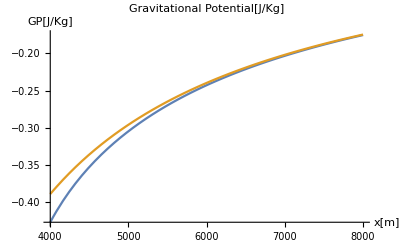

```mathematica
Plot[{V[x,0,0],Vm[x,0,0]},{x,4000,8000},PlotRange->All,AxesLabel->{"x[m]","GP[J/Kg]"},PlotLabel->"Gravitational Potential[J/Kg]"]
```

## Part 4: Landing on the Comet

## 5.

```mathematica
Subscript[r, lander][t_]={10000−(t/30)−(4×10^(−6))t^2,−5000+(t/1500)+(2*10^(-6))t^2,-6000+(t/1500)+(3*10^(-6))t^2};(*meters*)
```

```mathematica
Plot2=ParametricPlot3D[Subscript[r, lander][t],{t,0,42000}];
```

```mathematica
X[t_]=10000−(t/30)−(4*10^(−6))t^2;
Y[t_]=−5000+(t/1500)+(2*10^(-6))t^2;
Z[t_]=-6000+(t/1500)+(3*10^(-6))t^2;
Plot3=ParametricPlot3D[{X[t],Y[t],Z[t]},{t,0,10000},BoxRatios->{a/c,b/c,1}];
```

```mathematica
FindRoot[{(X[t]^2/a^2)+(Y[t]^2/b^2)+(Z[t]^2/c^2)==1},{t,10}](*this is correct*)
```

{t→41654.5}

```mathematica
Subscript[r, lander][41654.5]
Subscript[r, lander][0]
```

{1671.13,-1502.04,-766.938}

{10000,-5000,-6000}

```mathematica
Velocity[t_]=D[Subscript[r, lander][t],t]
```

{-1/30-t/125000,1/1500+t/250000,1/1500+(3 t)/500000}

```mathematica
massL=100;(*kg*)
```

```mathematica
N[41654/(60*60)]
```

11.5706

```mathematica
point1=Graphics3D[{White,Sphere[{1671.1271856666672,-1502.0355928333333,-766.9382225833324},300]}];
```

```mathematica
point2=Graphics3D[{Green,Sphere[{10000,-5000,-6000},600]}];
```

```mathematica
Show[Plot2,point1,point2,Plot1,PlotRange->{{10400,-7400},{-5400,5300},{-6300,3300}},PlotLabel->"Comet 1998P/Willis",AxesLabel->{"x(m)","y(m)","z(m)"}]
```

-Graphics3D-

## 6:

```mathematica
VInt=Norm[Velocity[0]](*velocity at launch in m/s*)
```

(√(139/2))/250

```mathematica
Subscript[mass, lander]=100;(*mass of lander in kg*)
```

```mathematica
GradVm[x_,y_,z_]=Grad[Vm[x,y,z],{x,y,z}];
GradVm[t_]=GradVm[X[t],Y[t],Z[t]];
force[t_]=-Subscript[mass, lander]*GradVm[t];
Subscript[force, i]=Norm[force[0]](*force initial*)
```

0.000850694

## 7(a-d):

```mathematica
VFin=Norm[Velocity[41654.5]](*veloctiy at impact in m/s*)
```

0.474504

The lander DOES in fact make a safe landing at a speed slower than 0.5 m/s

```mathematica
work1=(Subscript[PE, 0])-(Subscript[PE, f])(*joules*)
```

52.928

```mathematica
work2=-NIntegrate[Subscript[mass, lander]*GradVm[t].Velocity[t],{t,0,41654.5}](*in joules*)
```

52.928

```mathematica
VFREE=√(2*((Subscript[KE, 0]+Subscript[PE, 0])/Subscript[PE, f]))(*velocity in m/s*)
```

0.577241

## Total Energy:

```mathematica
Subscript[KE, 0]=(1/2)*(Subscript[mass, lander])*(VInt)^2;(*Kinetic energy initial in Kg*m^2/s^2*)
Subscript[PE, 0]=(Subscript[mass, lander])*(Vm[10000,-5000,-6000])(*Potential energy initial*)
Subscript[KE, f]=(1/2)*(Subscript[mass, lander])*(VFin)^2;(*Kentic energy final*);
Subscript[PE, f]=(Subscript[mass, lander])*(Vm[1671.1271856666672,-1502.0355928333333,-766.9382225833324])(*potential energy final*)
```

-10.6475

-63.5755

```mathematica
TotalEnergy=(Subscript[KE, f]+Subscript[PE, f])-(Subscript[KE, 0]+Subscript[PE, 0])-work1(*in J*)
```

-94.6538

## Orbiting in the coma:

```mathematica
p[t_]=4187.62 + (5812.38*Cos[0.0001t]);
q[t_]=1233.56 - (6233.56*Cos[0.0001t])+ (4499.51*Sin[0.0001t]);
s[t_]=-769.422-(5230.58*Cos[0.0001t])-(5362.31*Sin[0.0001t]);
Subscript[r, orbiter][t_] = {p[t], q[t], s[t]};
Plot3=ParametricPlot3D[Subscript[r, orbiter][t],{t,0,(2π)/0.0001}];
```

```mathematica
Show[Plot2,point1,point2,Plot1,Plot3,PlotRange->{{-10000,10300},{-8300,9300},{-8300,8300}},PlotLabel->"Comet 1998P/Willis",AxesLabel->{"x(m)","y(m)","z(m)"}]
```

-Graphics3D-

```mathematica
Subscript[V, dust][x_,y_,z_]=1.7*{ϵ^(-1.6*10^-9 x^2), ϵ^(-4*10^-8 y^2), ϵ^(-4*10^-8 z^2)};
Subscript[V, orbiter][t_]=D[Subscript[r, orbiter][t],t];
Subscript[T, orbit] = (2π)/0.0001;
Subscript[r, orbiter][0]
Subscript[r, orbiter][Subscript[T, orbit]]
Subscript[T, orbiter][t_]=(Subscript[V, orbiter][t])/Norm[Subscript[V, orbiter][t]];
Subscript[A, det]= 0.04;
Subscript[ρ, dust]_ = 2 * (10^(-6));
Subscript[V2, dust][t_] = Subscript[V, dust][p[t], q[t], s[t]];
Subscript[m, collect]= Subscript[A, det]*NIntegrate[Max[{0,(Subscript[V, orbiter][t]-Subscript[V2, dust][t]).Subscript[T, orbiter][t]}]*Subscript[ρ, dust],{t,0,Subscript[T, orbit]}]*1000
```

```mathematica
4.17958;(*amount of dust collected in grams*)
```